## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="FBP2";
fitLabel="";
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/MASSef/";
kineticDataFileName =  "kinetic_data_MASSef.csv";

mainFolder = "fit_FBP2_test";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

True

Working dir:/home/mrama/Dropbox/MASSef/examples/FBP2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{{{fdp,Null}},Keq substrate}

{41.5,Keq value}

{{{fdp,Null}},kcat substrates}

{5.7,kcat value}

{{{fdp,0.00006},{pep,0.001}},kcat substrates}

{3.22,kcat value}

{{{fdp,0.00005},{atp,0.00125}},kcat substrates}

{1.67,kcat value}

{{{fdp,0.00005},{adp,0.00125}},kcat substrates}

{0.949,kcat value}

{{{fdp,0.00005},{adp,0.0019}},kcat substrates}

{0.72,kcat value}

{fdp,Km or S05 substrate}

{0.00007,Km or S05 value}

{fdp,Other parameter susbtrate}

{2.05,Other parameter value}

{f1p,Inhibition or activation constant substrate}

{0.001,Inhibition or activation constant value}

{pi,Inhibition or activation constant substrate}

{0.00035,Inhibition or activation constant value}

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00007 | 0.000068
0.000072 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 5.7 | 5.6
5.8 | 1/s | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004
1 | fdp | 0.00006
pep | 0.001 | 9.66905 | 9.1856
10.1525 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
cl | 0.002
1 | fdp | 0.00005
atp | 0.00125 | 5.01469 | 4.76396
5.26543 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
1 | fdp | 0.00005
adp | 0.00125 | 2.84967 | 2.70718
2.99215 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001
1 | fdp | 0.00005
adp | 0.0019 | 2.16202 | 2.05392
2.27013 | 1/s | 7.7 | 37 | tric | 0.02 | mn2 | 0.001

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | f1p | 0.001 | 0.00095
0.00105 |  | Competitive | fdp | 0.00007 | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002
1 | Kic | pi | 0.00035 | 0.0003325
0.0003675 |  | Competitive | fdp | 0.00007 | M | 7.7 | 25 | tric | 0.02 | mn2 | 0.001
cl | 0.002

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | fdp | 2.05 | 2.
2.1 |  |  | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {};
s05Priorities = {1};
kcatPriorities = {1,0,0,0,0};
inhibitionPriorities={0,0};
activationPriorities = Null;
otherParamsPriorities = {1};


{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c+h2o^c→f6p^c+pi^c)^FBP2

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 41.5 | 39.425
43.575 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00007 | 0.000068
0.000072 |  | M | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 5.7 | 5.6
5.8 | 1/s | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | n | fdp | 2.05 | 2.
2.1 |  |  | 9 | 37 | chesk | 0.5 | mn2 | 0.002
cl | 0.004

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
enz ="E_FBP2[c]"
substrateList ={"fdp"};
productList={"pi", "f6p"};
nActiveSites = 2;
bindingReversibility = " <=> ";
releaseReversibility = " <=> ";
transitionReversibility = "<=> ";

catalyticBranch =generateOrderedMechanism[enz, substrateList,  productList, nActiveSites, bindingReversibility, 
						transitionReversibility, releaseReversibility] ;

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->1,Inhibitors->{},InhibitionSites->1];

catalyticBranch//TableForm
enzymeModelOrig["Reactions"]
```

E_FBP2[c]

E_FBP2[c] + fdp[c] <=> E_FBP2[c]&fdp
E_FBP2[c]&fdp + fdp[c] <=> E_FBP2[c]&fdp&fdp
E_FBP2[c]&fdp&fdp<=> E_FBP2[c]&pi&pi&f6p&f6p
E_FBP2[c]&pi&pi&f6p&f6p <=> E_FBP2[c]&pi&pi&f6p + f6p[c]
E_FBP2[c]&pi&pi&f6p <=> E_FBP2[c]&pi&pi + f6p[c]
E_FBP2[c]&pi&pi <=> E_FBP2[c]&pi + pi[c]
E_FBP2[c]&pi <=> E_FBP2[c] + pi[c]

{((FBP2^c)_^+fdp^c⇌(FBP2^c&fdp^c)_^)^FBP21,((FBP2^c&pi^c)_^⇌(FBP2^c)_^+pi^c)^FBP22,((FBP2^c&fdp^c)_^+fdp^c⇌(FBP2^c&fdp^c&fdp^c)_^)^FBP23,((FBP2^c&pi^c&pi^c)_^⇌(FBP2^c&pi^c)_^+pi^c)^FBP24,((FBP2^c&fdp^c&fdp^c)_^⇌(FBP2^c&pi^c&pi^c&f6p^c&f6p^c)_^)^FBP25,((FBP2^c&pi^c&pi^c&f6p^c)_^⇌(FBP2^c&pi^c&pi^c)_^+f6p^c)^FBP26,((FBP2^c&pi^c&pi^c&f6p^c&f6p^c)_^⇌(FBP2^c&pi^c&pi^c&f6p^c)_^+f6p^c)^FBP27}

### Define all catalytic tracks

```mathematica
catalyticReactionsSetsList = {enzymeModelOrig["Reactions"]};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=2;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, {},{}, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Loading flux equation...

Loading absolute rate forward equation...

Loading absolute rate reverse equation...

Loading relative rate forward equation...

Loading relative rate reverse equation...

Loading relative rate reverse equation...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModelOrig,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

```mathematica
FilePrint@dataPathList
```

Priority	f6p[c]	fdp[c]	pi[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	41.5
1	0	7.000000000000002e-6	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.00883377824981335
1	0	0.000011094252347227801	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.022395622457170455
1	0	0.00001758320502056708	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.055609816758203534
1	0	0.000027867501938744792	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.1314590000241482
1	0	0.000044167014113613516	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.28008099405284803
1	0	0.00007000000000000002	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.00011094252347227801	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.7199190059471522
1	0	0.0001758320502056708	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.8685409999758519
1	0	0.0002786750193874482	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9443901832417967
1	0	0.0004416701411361352	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9776043775428295
1	0	0.0007000000000000001	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9911662217501868
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	f6p[c]	fdp[c]	pi[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	40.44520383139027
1	0	6.681220703380521e-6	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.010008288260305101
1	0	0.000010589021210118044	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.024712420814393475
1	0	0.000016782467630742437	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.05971668328601667
1	0	0.000026598418700662637	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.13732197314049185
1	0	0.00004215565272891061	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.28519092739129753
1	0	0.0000668122070338052	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.49999999999999967
1	0	0.00010589021210118044	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.7148090726087021
1	0	0.00016782467630742438	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.8626780268595078
1	0	0.00026598418700662663	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9402833167139832
1	0	0.00042155652728910606	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9752875791856065
1	0	0.0006681220703380521	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9899917117396948
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.967801928775479

### Parameter scan

```mathematica
paramScanList={{"s05",1,{0.1,1,100}},
				{"kcat",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						 fitLabel,  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

Simulating Keq data...

Simulating S05 data...

Simulating kcat data...

Simulating other data...

```mathematica
FilePrint[dataPathList[[8]]]
```

Priority	f6p[c]	fdp[c]	pi[c]	param_FBP2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/haldaneRatio_1.txt"	0.1
1	0	7.000000000000002e-6	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.00883377824981335
1	0	0.000011094252347227801	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.022395622457170455
1	0	0.00001758320502056708	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.055609816758203534
1	0	0.000027867501938744792	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.1314590000241482
1	0	0.000044167014113613516	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.28008099405284803
1	0	0.00007000000000000002	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.00011094252347227801	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.7199190059471522
1	0	0.0001758320502056708	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.8685409999758519
1	0	0.0002786750193874482	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9443901832417967
1	0	0.0004416701411361352	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9776043775428295
1	0	0.0007000000000000001	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/relRateFor_fdp.txt"	0.9911662217501868
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7
1	0	1	0	1	9	37	"/home/mrama/Dropbox/MASSef/examples/FBP2/fit_FBP2_test/input/absRateFor.txt"	5.7

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=10;
numCPUs=1;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel, numCPUs];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel,numCPUs];
```

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.679994821737
best_fit: 0.888566466715
best_fit: 1.0107513909
best_fit: 1.09474113104
best_fit: 0.469616395839
best_fit: 0.899323096345
best_fit: 1.00862577927
best_fit: 0.655847152885
best_fit: 0.374313834564
best_fit: 0.898153657891

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, fitLabel<>"_"<>flagFitType];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | haldaneRatio_1 | 6.60121×10^-8 | 4.3576×10^-15 | 6.30794×10^-6 | 0.0000151998 | 41.5 | 41.5
1 | relRateFor_fdp | 0.0201815 | 0.000407293 | 0.00042019 | 4.75662 | 0.00883378 | 0.00925397
1 | relRateFor_fdp | 0.0101282 | 0.000102581 | 0.000528427 | 2.35951 | 0.0223956 | 0.022924
1 | relRateFor_fdp | 0.000338896 | 1.14851×10^-7 | 0.0000434114 | 0.0780643 | 0.0556098 | 0.0556532
1 | relRateFor_fdp | 0.00839162 | 0.0000704192 | 0.00251572 | 1.91369 | 0.131459 | 0.128943
1 | relRateFor_fdp | 0.0142414 | 0.000202817 | 0.00903547 | 3.22602 | 0.280081 | 0.271046
1 | relRateFor_fdp | 0.0150908 | 0.000227731 | 0.0170755 | 3.4151 | 0.5 | 0.482925
1 | relRateFor_fdp | 0.0114902 | 0.000132025 | 0.0187973 | 2.61103 | 0.719919 | 0.701122
1 | relRateFor_fdp | 0.00687361 | 0.0000472465 | 0.0136383 | 1.57025 | 0.868541 | 0.854903
1 | relRateFor_fdp | 0.00355127 | 0.0000126115 | 0.00769088 | 0.814375 | 0.94439 | 0.936699
1 | relRateFor_fdp | 0.00169549 | 2.87469×10^-6 | 0.00380914 | 0.38964 | 0.977604 | 0.973795
1 | relRateFor_fdp | 0.00077611 | 6.02347×10^-7 | 0.00176969 | 0.178546 | 0.991166 | 0.989397
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001
1 | absRateFor | 5.48236×10^-7 | 3.00563×10^-13 | 7.19546×10^-6 | 0.000126236 | 5.7 | 5.70001

### Simulated Data and Best Fit Data Plot

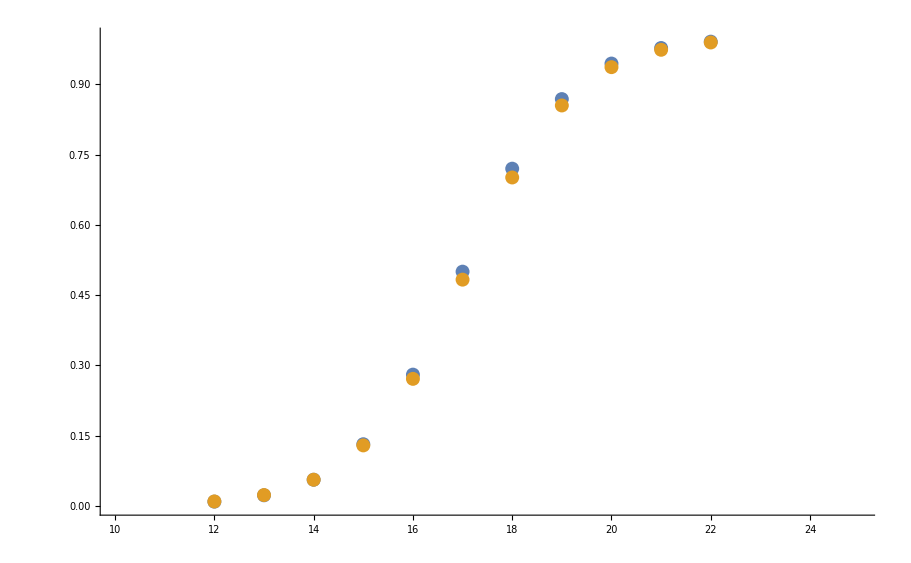

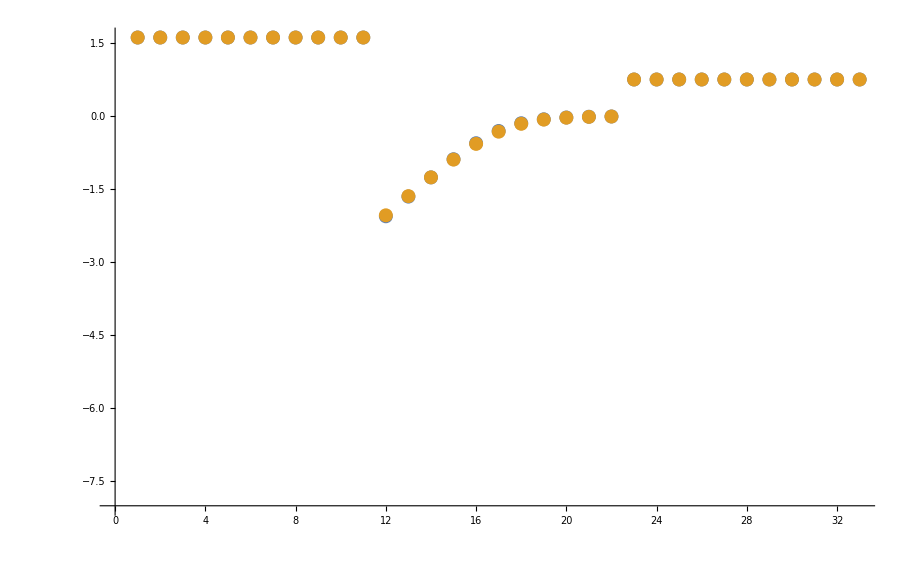

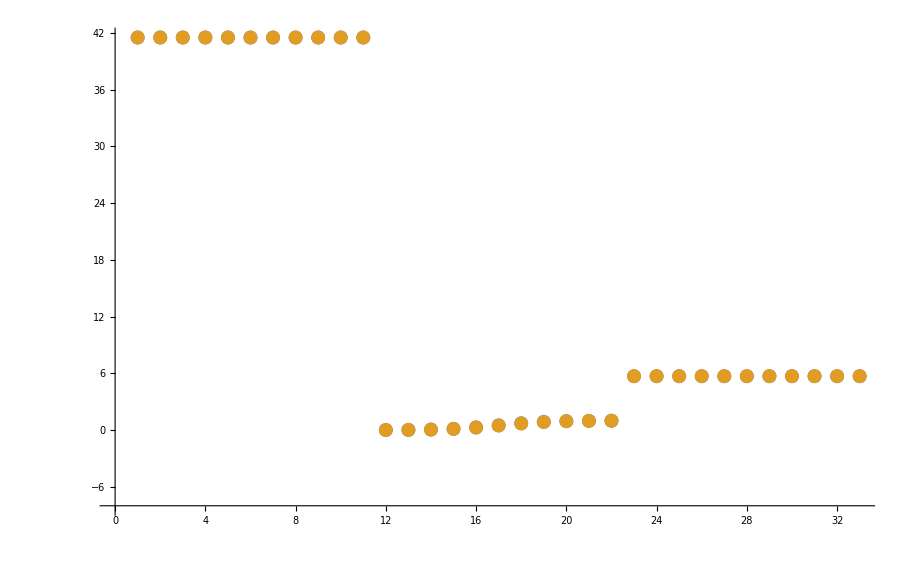

```mathematica
datasetI=1;
ListPlot[{fittingData[[All,-1]], filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}, PlotRange->{{10,25}, {0,1}}]
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[datasetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

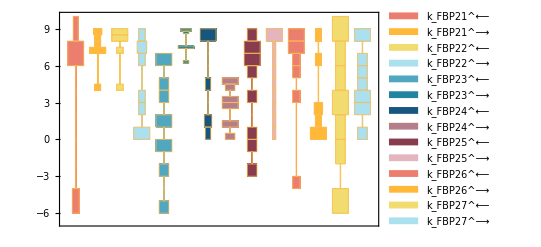

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

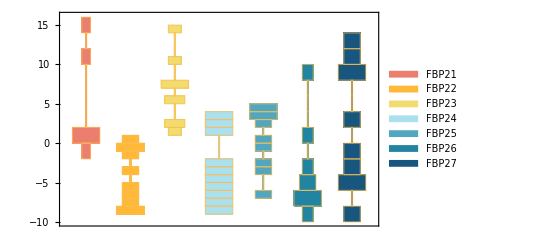

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

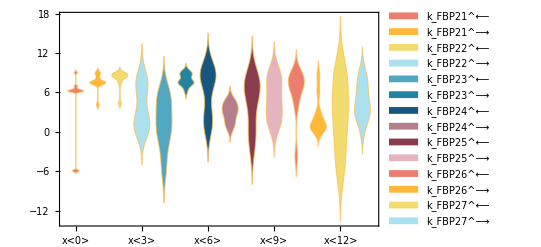

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

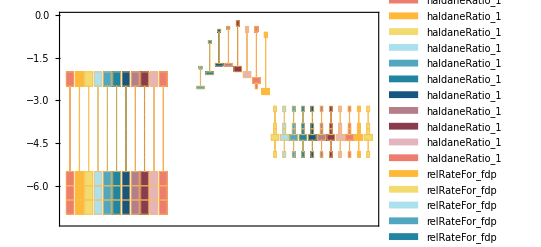

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
dataHeader = Import[dataFilePath][[1]];
```

```mathematica
backCalculateKms[rxn, s05List,relativeRateForward, relativeRateReverse, metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.00007 | 0.000072433 | 3.47564

```mathematica
backCalculateHillCoef[fittingData, filteredDataList[[paramSet]],dataHeader, s05List, otherParmsList]
```

{{data value,predicted value,error in %},{2.05,1.99806,2.53369}}

```mathematica
backCalculateKcats[rxn, kcatList,absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
5.7 | 5.6997 | 0.00519555

```mathematica
backCalculateRatios[haldaneRatiosList, KeqList[[All,3]],  paramFitSub]//TableForm
```

data value | predicted value | error in %
41.5 | 41.5 | 0.0000151998

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

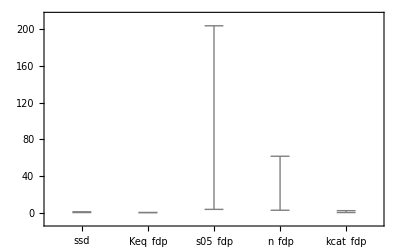

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```